```mathematica
state[1.01]
```

{0.0164095,-7.9081,0.,0.,0.}

```mathematica
Evaluate[x/.Solve[(height+x*Tan[pitch Degree])==0,x][[1]]]
```

-height Cot[° pitch]

```mathematica
state[1.012073]
```

{-5.07015×10^-6,-7.92844,0.,0.,0.}

```mathematica
hullLift[%]
```

100

```mathematica
InputForm[Evaluate[Which[
hullFront*Tan[-pitch Degree]≤ height &&  hullBack*Tan[-pitch Degree]≤ height,
0.0,
hullFront*Tan[-pitch Degree]> height &&  hullBack*Tan[-pitch Degree] > height,
Evaluate[Integrate[g*hullWidth*waterDensity*(height+x*Tan[pitch Degree]),{x,hullBack,hullFront}]],
hullFront*Tan[-pitch Degree]≤ height &&  hullBack*Tan[-pitch Degree]>height,
Evaluate[Integrate[g*hullWidth*waterDensity*(height+x*Tan[pitch Degree]),{x,hullBack,-(height*Cot[Degree*pitch])}]],
hullFront*Tan[-pitch Degree]>height &&  hullBack*Tan[-pitch Degree]≤ height,
Evaluate[Integrate[g*hullWidth*waterDensity*(height+x*Tan[pitch Degree]),{x,-(height*Cot[Degree*pitch]),hullFront}]]
]]]
```

Which[-(hullFront*Tan[Degree*pitch]) <= height && -(hullBack*Tan[Degree*pitch]) <= 
   height, 0, hullFront*Tan[(-pitch)*Degree] > height && 
  hullBack*Tan[(-pitch)*Degree] > height, -(g*height*hullBack*hullWidth*waterDensity) + 
  g*height*hullFront*hullWidth*waterDensity - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*pitch])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*pitch])/2, 
 hullFront*Tan[(-pitch)*Degree] <= height && hullBack*Tan[(-pitch)*Degree] > height, 
 -(g*height*hullBack*hullWidth*waterDensity) - 
  (g*height^2*hullWidth*waterDensity*Cot[Degree*pitch])/2 - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*pitch])/2, 
 hullFront*Tan[(-pitch)*Degree] > height && hullBack*Tan[(-pitch)*Degree] <= height, 
 g*height*hullFront*hullWidth*waterDensity + 
  (g*height^2*hullWidth*waterDensity*Cot[Degree*pitch])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*pitch])/2]

```mathematica
Which[-(hullFront*Tan[Degree*pitch]) <= height && -(hullBack*Tan[Degree*pitch]) <= 
   height, 0, hullFront*Tan[(-pitch)*Degree] > height && 
  hullBack*Tan[(-pitch)*Degree] > height, -(g*height*hullBack*hullWidth*waterDensity) + 
  g*height*hullFront*hullWidth*waterDensity - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*pitch])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*pitch])/2, 
 hullFront*Tan[(-pitch)*Degree] <= height && hullBack*Tan[(-pitch)*Degree] > height, 
 -(g*height*hullBack*hullWidth*waterDensity) - 
  (g*height^2*hullWidth*waterDensity*Cot[Degree*pitch])/2 - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*pitch])/2, 
 hullFront*Tan[(-pitch)*Degree] > height && hullBack*Tan[(-pitch)*Degree] <= height, 
 g*height*hullFront*hullWidth*waterDensity + 
  (g*height^2*hullWidth*waterDensity*Cot[Degree*pitch])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*pitch])/2]
```

```mathematica
hullLift[{0.0000001,0,0.,0.,0.}]
```

0

```mathematica
Plot3D[hullLift[{h,0,0.,a,0.}],{h,-5,5},{a,-60,60}]
```

-Graphics3D-

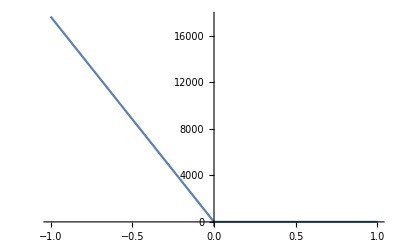

```mathematica
Plot[hullLift[{x,0,0.,0.,0.}],{x,-1,1}]
```

```mathematica
InputForm[Evaluate[x/.Solve[(height+x*Tan[pitch Degree])==0,x][[1]]]]
```

-(height*Cot[Degree*pitch])

```mathematica
x[a_][b_]:=a*b
```

```mathematica
c = x[5];
```

```mathematica
c[6]
```

30

```mathematica
Evaluate[Integrate[g*hullWidth*waterDensity*(height+x*Tan[pitch Degree]),{x,hullBack,-(height*Cot[Degree*pitch])}]]
```

-8829. height+1471.5 height^2 Cot[° pitch]+13243.5 Tan[° pitch]

```mathematica
Cot
```

```mathematica
-(g*height*hullBack*hullWidth*waterDensity) + 
  g*height*hullFront*hullWidth*waterDensity - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*pitch])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*pitch])/2
```

0.-17658. height

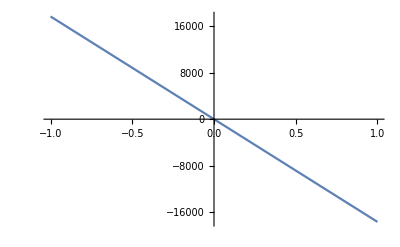

```mathematica
Plot[-(g*height*hullBack*hullWidth*waterDensity) + 
  g*height*hullFront*hullWidth*waterDensity - 
  (g*hullBack^2*hullWidth*waterDensity*Tan[Degree*0])/2 + 
  (g*hullFront^2*hullWidth*waterDensity*Tan[Degree*0])/2,{height,-1,1}]
```